### 1. naloga - prirejanje

Poiščimo najboljše prirejanje med delavci in službami.

```mathematica
v={s,Subscript[a, 1],Subscript[a, 2],Subscript[a, 3],Subscript[b, 1],Subscript[b, 2],Subscript[b, 3],Subscript[b, 4],t};
```

```mathematica
p={s->Subscript[a, 1],s->Subscript[a, 2],s->Subscript[a, 3],Subscript[a, 1]->Subscript[b, 2],Subscript[a, 1]->Subscript[b, 3],Subscript[a, 2]->Subscript[b, 1],Subscript[a, 2]->Subscript[b, 2],Subscript[a, 2]->Subscript[b, 3],Subscript[a, 2]->Subscript[b, 4],Subscript[a, 3]->Subscript[b, 1],Subscript[a, 3]->Subscript[b, 3],Subscript[b, 1]->t,Subscript[b, 2]->t,Subscript[b, 3]->t,Subscript[b, 4]->t};
c={1,1,1,4,4,4,4,4,4,4,4,1,1,1,1};
```

```mathematica
Length[p]==Length[c]
```

True

Esc + scG + Esc

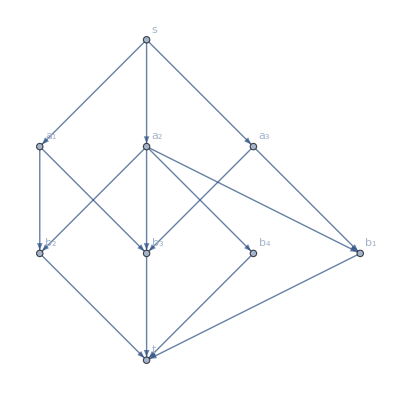

```mathematica
𝒢=Graph[v,p,EdgeCapacity->c,VertexLabels->"Name"]
```

```mathematica
ℱ=FindMaximumFlow[𝒢,s,t,"OptimumFlowData"]
```

OptimumFlowData[<9>, <9>]

```mathematica
ℱ["FlowValue"]
```

3

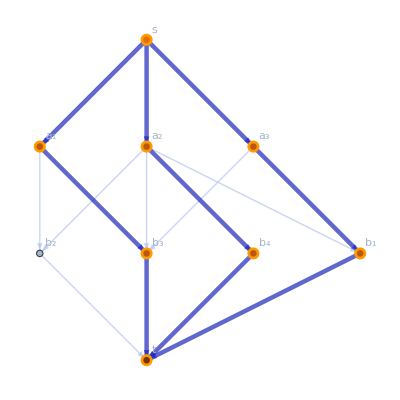

```mathematica
ℱ["FlowGraph"]
```

Kako bi si olajšali delo? Lahko naredimo funkcijo, ki iz matrike nariše graf.

```mathematica
(ma={{0,1,1,0},{1,1,1,1},{1,0,1,0}})//MatrixForm
m=First[Dimensions[ma]];
n=Last[Dimensions[ma]];
```

(0 | 1 | 1 | 0
1 | 1 | 1 | 1
1 | 0 | 1 | 0)

```mathematica
Clear[a]
```

```mathematica
v=Join[{s},Table[Subscript[a, i],{i,m}],Table[Subscript[b, j],{j,n}],{t}]
```

{s,a_1,a_2,a_3,b_1,b_2,b_3,b_4,t}

```mathematica
p=Join[Table[s->Subscript[a, i],{i,m}],Table[Subscript[b, j]->t,{j,n}]];
Do[If[ma[[i,j]]==1,AppendTo[p,Subscript[a, i]->Subscript[b, j]]],{i,m},{j,n}];
p
```

{s->a_1,s->a_2,s->a_3,b_1->t,b_2->t,b_3->t,b_4->t,a_1->b_2,a_1->b_3,a_2->b_1,a_2->b_2,a_2->b_3,a_2->b_4,a_3->b_1,a_3->b_3}

```mathematica
c=Join[Table[1,{m+n}],
Table[m+1,{Length[p]-(m+n)}]]
```

{1,1,1,1,1,1,1,4,4,4,4,4,4,4,4}

```mathematica
{1,1,1,1,1,1,1,4,4,4,4,4,4,4,4}
```

{1,1,1,1,1,1,1,4,4,4,4,4,4,4,4}

```mathematica
𝒢=Graph[v,p,EdgeCapacity->c,VertexLabels->"Name"]
```

-Graphics-

```mathematica
ℱ=FindMaximumFlow[𝒢,s,t,"OptimumFlowData"]
```

OptimumFlowData[<9>, <9>]

```mathematica
ℱ["FlowValue"]
```

3

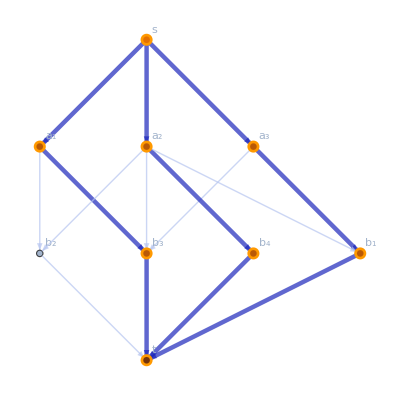

```mathematica
ℱ["FlowGraph"]
```

Sedaj si upamo reševati kompleksnejši problem. Naredimo najprej funkcijo.

```mathematica
GrafPrireditve[ma_]:=Module[{m,n,v,p,c},
m=First[Dimensions[ma]];
n=Last[Dimensions[ma]];
v=Join[{s},Table[Subscript[a, i],{i,m}],Table[Subscript[b, j],{j,n}],{t}];
p=Join[Table[s->Subscript[a, i],{i,m}],Table[Subscript[b, j]->t,{j,n}]];
Do[If[ma[[i,j]]==1,AppendTo[p,Subscript[a, i]->Subscript[b, j]]],{i,m},{j,n}];
c=Join[Table[1,{m+n}],Table[m+1,{Length[p]-(m+n)}]] ;
Graph[v,p,EdgeCapacity->c,VertexLabels->"Name"]]
```

```mathematica
ℱ=FindMaximumFlow[GrafPrireditve[ma],s,t,"OptimumFlowData"]
```

OptimumFlowData[<9>, <9>]

```mathematica
ℱ[FlowValue]
```

3

```mathematica
ℱ[FlowGraph]
```

-Graphics-

Poskusimo na naključni matriki.

```mathematica
(ma =Table[RandomInteger[{0,1}],{10},{10}])//MatrixForm
```

(0 | 0 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
0 | 0 | 1 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 1 | 0 | 1 | 0 | 0 | 0
0 | 1 | 0 | 0 | 1 | 0 | 1 | 1 | 0 | 1
0 | 0 | 0 | 1 | 1 | 0 | 1 | 0 | 1 | 0
0 | 0 | 1 | 1 | 1 | 0 | 1 | 1 | 0 | 0
0 | 1 | 0 | 1 | 0 | 1 | 0 | 0 | 0 | 1
1 | 0 | 1 | 1 | 0 | 1 | 1 | 1 | 1 | 1
1 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | 0
0 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0)

OptimumFlowData[<22>, <30>]

10

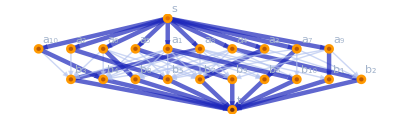

```mathematica
ℱ=FindMaximumFlow[GrafPrireditve[ma],s,t,"OptimumFlowData"]
ℱ[FlowValue]
ℱ[FlowGraph]
```

Obstaja še bližnjica.

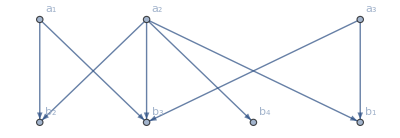

```mathematica
v={Subscript[a, 1],Subscript[a, 2],Subscript[a, 3],Subscript[b, 1],Subscript[b, 2],Subscript[b, 3],Subscript[b, 4]};
p={Subscript[a, 1]->Subscript[b, 2],Subscript[a, 1]->Subscript[b, 3],Subscript[a, 2]->Subscript[b, 1],Subscript[a, 2]->Subscript[b, 2],Subscript[a, 2]->Subscript[b, 3],Subscript[a, 2]->Subscript[b, 4],Subscript[a, 3]->Subscript[b, 1],Subscript[a, 3]->Subscript[b, 3]};
𝒢=Graph[v,p,VertexLabels->"Name"]
```

```mathematica
ℱ=FindMaximumFlow[𝒢,{Subscript[a, 1],Subscript[a, 2],Subscript[a, 3]},{Subscript[b, 1],Subscript[b, 2],Subscript[b, 3],Subscript[b, 4]},"OptimumFlowData",VertexCapacity->ConstantArray[1,7]]
```

FindMaximumFlow[𝒢,{a_1,a_2,a_3},{b_1,b_2,b_3,b_4},OptimumFlowData,VertexCapacity→{1,1,1,1,1,1,1}]

To zgoraj še ne dela. Profesor bo dopolnil na spletni učilnici. Bližnjica je v tem, da ni treba navesti povezav od izvora in tistih do ponora.

### Problem popolnega prirejanja